```mathematica
ℏ=1;
d=1;
Subscript[k, 0]=1;
tmax=2;
m=1;
A=√(1/(d √π));
ρ[x_,t_]=A^2/(√(1+((ℏ t)/(m d^2))^2))Exp[-(x-(ℏ Subscript[k, 0])/m t)^2/(d^2(1+((ℏ t)/(m d^2))^2))];
Manipulate[Plot[ρ[x,t],{x,-3,5},PlotRange->{0,0.6}],{ t,0,tmax}]
```

```mathematica
ΔQ[t_]=∫_(-∞)^∞ x^2 ρ[x,t]ⅆx-(∫_(-∞)^∞ x ρ[x,t]ⅆx)^2;
ΔQ[t_]=Simplify[%,t>0]
```

1/2 (1+t^2)

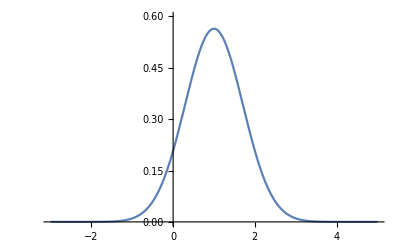

```mathematica
Φ[p_,t_]=d/(ℏ √π)ⅇ^(-d^2/ℏ^2(p-ℏ Subscript[k, 0])^2);
Plot[Φ[p,t],{p,-3,5},PlotRange->{0,0.6}]
```

```mathematica
ΔP=∫_(-∞)^∞ p^2 Φ[p,t]ⅆp-(∫_(-∞)^∞ p Φ[p,t]ⅆp)^2
```

1/2

1/4 (1+t^2)

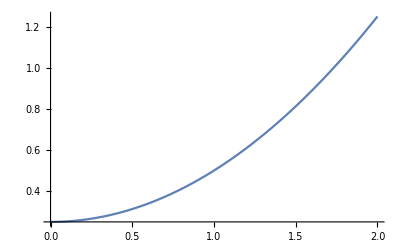

```mathematica
ΔQ ΔP
Plot[ΔQ ΔP,{t,0,tmax}]
```